# Gaussian Kernel basis vs Newtonized Gaussian Kernel basis

## A Somewhat different Perspective

I started to make this notebook last week after talking with Palmer about the search for a closed form. I haven’t finished it yet however.

## Introduction

First, we will look at a simple differential equation taken from Trefethen’s book on spectral methods first using the usual Gaussian kernel basis. Then, following Shaback’s formalism and Fasshauer’s suggestion, we will endeavor to solve this differential equation using the Newtonized version of this basis.

Remark: There is a fair amount of excessive explanation going on and redundant Mathematica as well since neither of you knows this language and I figured you could learn some Mathematica if I took this more pedagogic approach. I am not trying to convert anybody to Mathematica as I have discovered this is an exercise in futility!

## Gaussian Kernel Basis

The differential equation we will solve is the boundary value problem given by u''(x)=ⅇ^(4x)  u(-1)=u(1)=0. The exact solution can be calculated easily.

```mathematica
sol=u[x]/.DSolve[{u''[x]==Exp[4x],u[-1]==0,u[1]==0},u[x],x][[1]]
```

-(1+ⅇ^8-2 ⅇ^(4+4 x)-x+ⅇ^8 x)/(32 ⅇ^4)

In order to solve this numerically, first we set up our interpolant using n=8 , or, in other words, 7 interior points and 2 boundary points for a total of 9 data points.

```mathematica
data=Most[Rest[Range[-1,1,1/4]//N]]
```

{-0.75,-0.5,-0.25,0.,0.25,0.5,0.75}

Now we create our interpolant. Note that we need to add two additional degrees of freedom to guarantee that we have can satisfy our boundary condtions.

```mathematica
u[x_,ϵ_]:=Sum[c[j] ⅇ^(-ϵ (x-data[[j]])^2),{j,1,7}]+a+b x
```

Now we construct our second derivative function.

```mathematica
d2u[x_,ϵ_]=D[u[x,ϵ],{x,2}]
```

(-2 ⅇ^(-(0.75+x)^2 ϵ) ϵ+4 ⅇ^(-(0.75+x)^2 ϵ) (0.75+x)^2 ϵ^2) c[1]+(-2 ⅇ^(-(0.5+x)^2 ϵ) ϵ+4 ⅇ^(-(0.5+x)^2 ϵ) (0.5+x)^2 ϵ^2) c[2]+(-2 ⅇ^(-(0.25+x)^2 ϵ) ϵ+4 ⅇ^(-(0.25+x)^2 ϵ) (0.25+x)^2 ϵ^2) c[3]+(-2 ⅇ^(-(0.+x)^2 ϵ) ϵ+4 ⅇ^(-(0.+x)^2 ϵ) (0.+x)^2 ϵ^2) c[4]+(-2 ⅇ^(-(-0.25+x)^2 ϵ) ϵ+4 ⅇ^(-(-0.25+x)^2 ϵ) (-0.25+x)^2 ϵ^2) c[5]+(-2 ⅇ^(-(-0.5+x)^2 ϵ) ϵ+4 ⅇ^(-(-0.5+x)^2 ϵ) (-0.5+x)^2 ϵ^2) c[6]+(-2 ⅇ^(-(-0.75+x)^2 ϵ) ϵ+4 ⅇ^(-(-0.75+x)^2 ϵ) (-0.75+x)^2 ϵ^2) c[7]

Now we create the left hand sides of our interpolation equations.

```mathematica
d2u[#,1]&/@data
```

{-2. c[1]-1.64397 c[2]-0.778801 c[3]+0.142446 c[4]+0.735759 c[5]+0.890848 c[6]+0.737795 c[7],-1.64397 c[1]-2. c[2]-1.64397 c[3]-0.778801 c[4]+0.142446 c[5]+0.735759 c[6]+0.890848 c[7],-0.778801 c[1]-1.64397 c[2]-2. c[3]-1.64397 c[4]-0.778801 c[5]+0.142446 c[6]+0.735759 c[7],0.142446 c[1]-0.778801 c[2]-1.64397 c[3]-2. c[4]-1.64397 c[5]-0.778801 c[6]+0.142446 c[7],0.735759 c[1]+0.142446 c[2]-0.778801 c[3]-1.64397 c[4]-2. c[5]-1.64397 c[6]-0.778801 c[7],0.890848 c[1]+0.735759 c[2]+0.142446 c[3]-0.778801 c[4]-1.64397 c[5]-2. c[6]-1.64397 c[7],0.737795 c[1]+0.890848 c[2]+0.735759 c[3]+0.142446 c[4]-0.778801 c[5]-1.64397 c[6]-2. c[7]}

Now we create the right hand sides of our interpolation equations.

```mathematica
newVals=Rest[Most[Exp[4#]&/@(Range[-1,1,1/4]//N)]]
```

{0.0497871,0.135335,0.367879,1.,2.71828,7.38906,20.0855}

Now we put the lhs and rhs together using Thread. This is a nice function in Mathematica.

```mathematica
Thread[d2u[#,1]&/@data==newVals]
```

{-2. c[1]-1.64397 c[2]-0.778801 c[3]+0.142446 c[4]+0.735759 c[5]+0.890848 c[6]+0.737795 c[7]==0.0497871,-1.64397 c[1]-2. c[2]-1.64397 c[3]-0.778801 c[4]+0.142446 c[5]+0.735759 c[6]+0.890848 c[7]==0.135335,-0.778801 c[1]-1.64397 c[2]-2. c[3]-1.64397 c[4]-0.778801 c[5]+0.142446 c[6]+0.735759 c[7]==0.367879,0.142446 c[1]-0.778801 c[2]-1.64397 c[3]-2. c[4]-1.64397 c[5]-0.778801 c[6]+0.142446 c[7]==1.,0.735759 c[1]+0.142446 c[2]-0.778801 c[3]-1.64397 c[4]-2. c[5]-1.64397 c[6]-0.778801 c[7]==2.71828,0.890848 c[1]+0.735759 c[2]+0.142446 c[3]-0.778801 c[4]-1.64397 c[5]-2. c[6]-1.64397 c[7]==7.38906,0.737795 c[1]+0.890848 c[2]+0.735759 c[3]+0.142446 c[4]-0.778801 c[5]-1.64397 c[6]-2. c[7]==20.0855}

Now we add in our boundary values

```mathematica
Reduce[u[-1,1]==0&&u[1,1]==0&&And@@Thread[d2u[#,1]&/@data==newVals]]
```

c[7]==-637.374&&c[6]==2201.5&&c[5]==-3929.68&&c[4]==4409.19&&c[3]==-3300.32&&c[2]==1550.73&&c[1]==-375.694&&b==11.0163&&a==36.1345

Now we create rules from these solutions

```mathematica
ToRules[Reduce[u[-1,1]==0&&u[1,1]==0&&And@@Thread[d2u[#,1]&/@data==newVals]]]
```

{c[7]→-637.374,c[6]→2201.5,c[5]→-3929.68,c[4]→4409.19,c[3]→-3300.32,c[2]→1550.73,c[1]→-375.694,b→11.0163,a→36.1345}

Now we apply those rules to create our solution

```mathematica
u[x,1]/.ToRules[Reduce[u[-1,1]==0&&u[1,1]==0&&And@@Thread[(d2u[#,1]&/@data)==(Exp[4#]&/@data)]]]
```

36.1345-637.374 ⅇ^(-(-0.75+x)^2)+2201.5 ⅇ^(-(-0.5+x)^2)-3929.68 ⅇ^(-(-0.25+x)^2)+4409.19 ⅇ^(-(0.+x)^2)-3300.32 ⅇ^(-(0.25+x)^2)+1550.73 ⅇ^(-(0.5+x)^2)-375.694 ⅇ^(-(0.75+x)^2)+11.0163 x

All of this can be zipped up into a single function solve. Note that we leave the kernel, and the differential equation as “hard coded”, but it should be easy to create a generic solver from this code.

```mathematica
Clear[solve]
```

```mathematica
solve[n_,ϵ_]:=Module[{data,u,d2u,c,a,b},
data=Most[Rest[Range[-1,1,1/n]//N]];
u[x_,α_]=Sum[c[j] ⅇ^(-α(x-data[[j]])^2),{j,1,2n-1}]+a+b x;
d2u[x_,α_]=D[u[x,α],{x,2}];
u[x,ϵ]/.ToRules[Reduce[u[-1,ϵ]==0&&u[1,ϵ]==0&&And@@Thread[(d2u[#,ϵ]&/@data)==(Exp[4#]&/@data)]]]]
```

Now we test this code.

```mathematica
f=solve[4,1]
```

36.1345-637.374 ⅇ^(-(-0.75+x)^2)+2201.5 ⅇ^(-(-0.5+x)^2)-3929.68 ⅇ^(-(-0.25+x)^2)+4409.19 ⅇ^(-(0.+x)^2)-3300.32 ⅇ^(-(0.25+x)^2)+1550.73 ⅇ^(-(0.5+x)^2)-375.694 ⅇ^(-(0.75+x)^2)+11.0163 x

Good the same answer! We may plot our approximate solution of course.

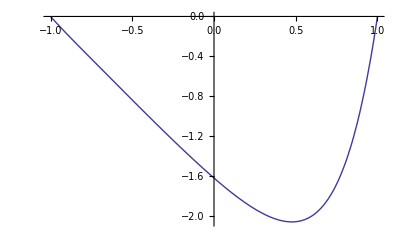

```mathematica
Plot[f,{x,-1,1}]
```

We may plot the approximate solution and the exact solution

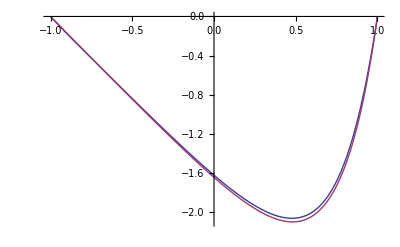

```mathematica
Plot[{f,sol},{x,-1,1}]
```

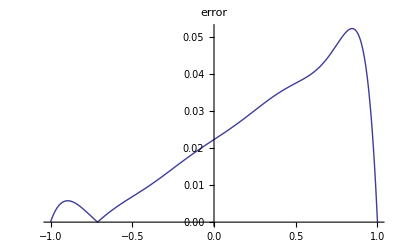

```mathematica
Plot[Abs[f-sol],{x,-1,1},PlotLabel-> "error"]
```

We may include the plotting in a modifed routine of course.

```mathematica
solvePlot[n_,ϵ_]:=Module[{data,u,d2u,c,a,b},
data=Most[Rest[Range[-1,1,1/n]//N]];
u[x_,α_]=Sum[c[j] ⅇ^(-α(x-data[[j]])^2),{j,1,2n-1}]+a+b x;
d2u[x_,α_]=D[u[x,α],{x,2}];
sol=u[x,ϵ]/.ToRules[Reduce[u[-1,ϵ]==0&&u[1,ϵ]==0&&And@@Thread[(d2u[#,ϵ]&/@data)==(Exp[4#]&/@data)]]];
Plot[{sol,-(1+ⅇ^8-2 ⅇ^(4+4 x)-x+ⅇ^8 x)/(32 ⅇ^4)},{x,-1,1}]]
```

Which we may immediately turn into a Manipulate!

```mathematica
Manipulate[solvePlot[n,ϵ],{{n,4},2,20,1},{{ϵ,1},.1,10}]
```

And now we can play around! You will note it is fairly easy to break this, but for small values of n it should work. You will note that as n gets larger you need to localize the kernel more by increasing ϵ or you start to get condition warnings. This is a manifestation of a type of “uncertainty principle” in kernel approximation I think. This notion was developed by Schaback, but I seem to recall he is sort of revising it. We’ll ask Greg about this as I think this is a recent development and perhaps is related to Greg’s HS research which says don’t even bother forming the K matrix!? Finally, you will also note that you can still get nice looking results with bad condition numbers, but eventually this whole process breaks down.

Finally, a big point about how this was programmed. There is both a strength and a weakness to how this was programmed. The strength is that it  was easy! Note that I never formed any matrix myself. I let Reduce detect that it had a linear system on its hands and it passed the problem to LinearSolve which passed it on to other routines like RowReduce so you are still solving a linear system--this has simply been abstracted away in the above code. The big weakness is that we only start to see condition number warnings when things go awry and that’s bad because condition numbers are the main thing we care about. In other words, to make this more useful we would need to figure out the actual matrices being used or some way for Mathematica to spit out condition numbers all the time. This is probably possible I think. Incidentally, this is one reason I told you Palmer that I did not recall encountering any condition number problems on Monday --I had only done this for n=4 and 5 with ϵ=1.

## Newtonized Gaussian Kernel basis

Haven’t done this yet, been working with Sergey all day. The truth is that the only value in what has been presented thus far is that if we decided we actually wanted to obtain a closed form for the Newtonized Gaussian basis, we might be able to using Mathematica without much difficulty if we get lucky!